# One-Way Quantum Computation

```mathematica
<<Q3`
```

## Elementary Idea: Rotation Z(ϕ)

```mathematica
Let[Qubit,S]
```

```mathematica
Let[Real,α,β,γ]
Let[Complex,c]
```

```mathematica
R0=Rotation[α,S[0,3],Label->"R"];
v0=ProductState[S[0]->{c[0],c[1]},S[1]->{1,0}]
rules={c[{0,1}].Dagger@c[{0,1}]->1};
```

(c_(,,0) 0+c_(,,1) 1)_(S_(,,0))⊗(0)_(S_(,,1))

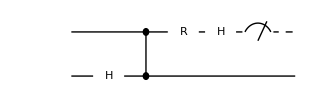

```mathematica
qc=QuantumCircuit[
v0,
S[1,6],
CZ[S[0],S[1]],R0,
S[0,6],Measurement[S[0,3]],
"PortSize"->{2,1}
]
```

```mathematica
v=Elaborate[qc]
```

1/2 ⅇ^(-(ⅈ α)/2) (c_(,,0)+ⅇ^(ⅈ α) c_(,,1)) 0_(,,S_(,,0))0_(,,S_(,,1))+1/2 ⅇ^(-(ⅈ α)/2) (c_(,,0)-ⅇ^(ⅈ α) c_(,,1)) 0_(,,S_(,,0))1_(,,S_(,,1))

```mathematica
v=v/.rules//Simplify
vv=KetFactor[v,S[0]]//Simplify
w=vv[[2]]
```

1/2 ⅇ^(-(ⅈ α)/2) ((c_(,,0)+ⅇ^(ⅈ α) c_(,,1)) 0_(,,S_(,,0))0_(,,S_(,,1))+(c_(,,0)-ⅇ^(ⅈ α) c_(,,1)) 0_(,,S_(,,0))1_(,,S_(,,1)))

0_(,,S_(,,0))⊗(1/2 ⅇ^(-(ⅈ α)/2) ((c_(,,0)+ⅇ^(ⅈ α) c_(,,1)) 0_(,,S_(,,1))+(c_(,,0)-ⅇ^(ⅈ α) c_(,,1)) 1_(,,S_(,,1))))

1/2 ⅇ^(-(ⅈ α)/2) ((c_(,,0)+ⅇ^(ⅈ α) c_(,,1)) 0_(,,S_(,,1))+(c_(,,0)-ⅇ^(ⅈ α) c_(,,1)) 1_(,,S_(,,1)))

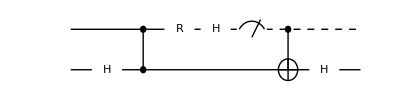

```mathematica
qc=QuantumCircuit[
v0,
S[1,6],CZ[S[0],S[1]],
R0,S[0,6],
Measurement[S[0,3]],
CNOT[S[0],S[1]],S[1,6],
"PortSize"->{2,1}
]
```

```mathematica
v1=Elaborate[qc]/.rules//Simplify
v1=KetFactor[v1,S[0]][[2]]
```

(ⅇ^(-(ⅈ α)/2) (c_(,,0) 0_(,,S_(,,0))0_(,,S_(,,1))+ⅇ^(ⅈ α) c_(,,1) 0_(,,S_(,,0))1_(,,S_(,,1))))/(√2)

(ⅇ^(-(ⅈ α)/2) c_(,,0) 0_(,,S_(,,1)))/(√2)+(ⅇ^((ⅈ α)/2) c_(,,1) 1_(,,S_(,,1)))/(√2)

```mathematica
v2=Rotation[α,S[1,3]]**ProductState[S[1]->c@{0,1}]//Elaborate;
v2-v1//Simplify
```

-1/2 (-2+√2) ⅇ^(-(ⅈ α)/2) (c_(,,0) 0_(,,S_(,,1))+ⅇ^(ⅈ α) c_(,,1) 1_(,,S_(,,1)))

## General Single-Qubit Rotations

```mathematica
Let[Qubit,S]
Let[Real,α,β,γ]
Let[Complex,c]
```

```mathematica
R1=Rotation[α,S[1,3],Label->"R"];
R2=Rotation[β,S[2,3],Label->Superscript["R",′]];
R3=Rotation[γ,S[3,3],Label->Superscript["R",″]];
```

```mathematica
jj=Range[4]
kk=Range[0,4]
SS=S[kk,None]
```

{1,2,3,4}

{0,1,2,3,4}

{S_(,,0),S_(,,1),S_(,,2),S_(,,3),S_(,,4)}

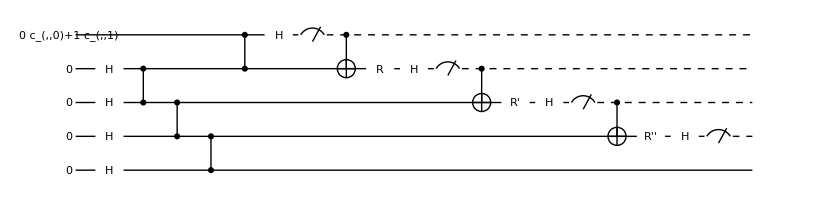

```mathematica
qc=QuantumCircuit[
ProductState[S[0]->{c[0],c[1]},S[{1,2,3,4}]->{1,0}],
S[jj,6],
CZ[S[1],S[2]],CZ[S[2],S[3]],CZ[S[3],S[4]],
CZ[S[0],S[1]],
S[0,6],Measurement[S[0,3]],
CNOT[S[0],S[1]],R1,
S[1,6],Measurement[S[1,3]],
CNOT[S[1],S[2]],R2,
S[2,6],Measurement[S[2,3]],
CNOT[S[2],S[3]],R3,
S[3,6],Measurement[S[3,3]],
"PortSize"->{2,1}
]
```

```mathematica
Timing[mat=Matrix[qc];]
expr=ExpressionFor[mat,SS]/.{c[0]Conjugate[c[0]]+c[1]Conjugate[c[1]]->1}
```

Measurement::num: Probability half is assumed for a state without explicitly numeric coefficients.

{0.704301,Null}

1/16 ⅇ^(-1/2 ⅈ (α+β+γ)) ((1+ⅇ^(ⅈ α)-ⅇ^(ⅈ β)+ⅇ^(ⅈ (α+β))+ⅇ^(ⅈ γ)+ⅇ^(ⅈ (α+γ))+ⅇ^(ⅈ (β+γ))-ⅇ^(ⅈ (α+β+γ))) c_(,,0)+(1-ⅇ^(ⅈ α)-ⅇ^(ⅈ β)-ⅇ^(ⅈ (α+β))+ⅇ^(ⅈ γ)-ⅇ^(ⅈ (α+γ))+ⅇ^(ⅈ (β+γ))+ⅇ^(ⅈ (α+β+γ))) c_(,,1)) 1_(,,S_(,,0))1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))0_(,,S_(,,4))+1/16 ⅇ^(-1/2 ⅈ (α+β+γ)) ((-1-ⅇ^(ⅈ α)+ⅇ^(ⅈ β)-ⅇ^(ⅈ (α+β))+ⅇ^(ⅈ γ)+ⅇ^(ⅈ (α+γ))+ⅇ^(ⅈ (β+γ))-ⅇ^(ⅈ (α+β+γ))) c_(,,0)+(-1+ⅇ^(ⅈ α)+ⅇ^(ⅈ β)+ⅇ^(ⅈ (α+β))+ⅇ^(ⅈ γ)-ⅇ^(ⅈ (α+γ))+ⅇ^(ⅈ (β+γ))+ⅇ^(ⅈ (α+β+γ))) c_(,,1)) 1_(,,S_(,,0))1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))1_(,,S_(,,4))

## Magic State Injection

Unlike the Clifford gates, the so-called T-gate (a phase gate by phase angle ϕ=2π/8) turns out to be difficult to implement in a fault-tolerant way. As a workaround, magic state injection method has been suggested. It is a special case of the measurement-based quantum computing.

```mathematica
Let[Qubit,S]
Let[Real,ϕ]
Let[Complex,c]
```

First, generate the magic state ϕ. Of course, we are interested in the case of ϕ=2π/8, i.e., ϕ=2π/8≡T.

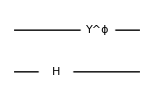

((1+ⅇ^(ⅈ ϕ)) 0_(,,S)0_(,,S_(,,2)))/(2 √2)+((1+ⅇ^(ⅈ ϕ)) 0_(,,S)1_(,,S_(,,2)))/(2 √2)-(ⅈ (-1+ⅇ^(ⅈ ϕ)) 1_(,,S)0_(,,S_(,,2)))/(2 √2)-(ⅈ (-1+ⅇ^(ⅈ ϕ)) 1_(,,S)1_(,,S_(,,2)))/(2 √2)

```mathematica
mgc=QuantumCircuit[Ket[S@{2}],S[2,6],Phase[ϕ,S[2]]]
Elaborate[mgc]
```

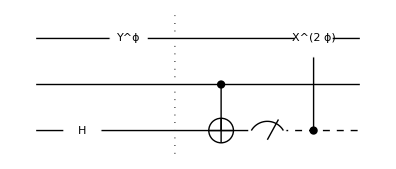

```mathematica
in=ProductState[S[1]->c@{0,1},"Label"->Ket[{ψ}]];
qc=QuantumCircuit[in,mgc,"Separator",
CNOT[S[1],S[2]],Measurement[S[2,3]],
ControlledGate[S[2],Phase[2ϕ,S[1]]],
ProductState[S[1]->{c[0],c[1]*Exp[I*ϕ]},"Label"->DisplayForm@RowBox@{Superscript["Z","ϕ"],Ket[{ψ}]}],
"PortSize"->{1,3}
]
```

Check that regardless of the measurement result, the state prepared in the first qubit (up to a global phase) becomes the desired state Z^ϕ ψ.

```mathematica
out=Elaborate[qc]//Simplify;
KetFactor@LogicalForm[out,S@{1,2}]
```

Q3General::renamed: Symbol LogicalForm has been renamed KetRegulate.

1/(√2)(1/4+ⅈ/4) (0_(,,S)-ⅈ ⅇ^(ⅈ ϕ) 0_(,,S)-ⅈ ⅇ^(2 ⅈ ϕ) 0_(,,S)+ⅇ^(3 ⅈ ϕ) 0_(,,S)+1_(,,S)-ⅈ ⅇ^(ⅈ ϕ) 1_(,,S)+ⅈ ⅇ^(2 ⅈ ϕ) 1_(,,S)-ⅇ^(3 ⅈ ϕ) 1_(,,S))⊗(c_(,,0) 0_(,,S_(,,1))+c_(,,1) 1_(,,S_(,,1)))⊗1_(,,S_(,,2))